## Definitions

```mathematica
<<SimulationTools`
```

```mathematica
evalOnGrid[expr_,{t_,x_,y_,z_},d_DataRegion]:=
Module[{xd,yd,zd,td},
{xd,yd,zd}=Table[GetCoordinate[d,i],{i,3}];
td=GetTime[d];
expr/.{x->xd,y->yd,z->zd,t->td}]
```

## Parameters

```mathematica
id={a->0.1,d->1/Sqrt[3],psi->-1.9216757376671543544,theta->0.66214523564555227398,phi->1.2199169159226388841};
```

```mathematica
{runLow,runHigh}={"sgw3d_Carlile_ord4_15","sgw3d_Carlile_ord4_30"}
```

{sgw3d_Carlile_ord4_15,sgw3d_Carlile_ord4_30}

```mathematica
order=4; (* Change this for different order tests *)
```

```mathematica
var="g"; (* This can be g or k *)
```

```mathematica
comp={1,1}; (* This is the tensor component, so 1,1 is xx *)
```

```mathematica
dirs={"x","y","z"};
```

```mathematica
varName=var<>dirs[[comp[[1]]]]<>dirs[[comp[[2]]]]
```

gxx

```mathematica
file=varName<>".h5"
```

gxx.h5

```mathematica
i=30; (* Consider the ith common iteration (i = 0 is initial data, i = 1 is first common iteration) *)
```

```mathematica
itLow=30;
```

```mathematica
itHigh=60;
```

## Gauge wave exact solution

```mathematica
Hp=a Sin[2Pi(xp-t)/d]
```

a Sin[(2 π (-t+xp))/d]

```mathematica
HpDot=D[Hp,t]
```

-(2 a π Cos[(2 π (-t+xp))/d])/d

```mathematica
gpxx=1+Hp
```

1+a Sin[(2 π (-t+xp))/d]

```mathematica
kpxx=HpDot/(2Sqrt[1+Hp])
```

-(a π Cos[(2 π (-t+xp))/d])/(d √(1+a Sin[(2 π (-t+xp))/d]))

```mathematica
(gp=Table[If[i==1&&j==1,gpxx,If[i==j,1,0]],{i,3},{j,3}])//MatrixForm
```

(1+a Sin[(2 π (-t+xp))/d] | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
(kp=Table[If[i==1&&j==1,kpxx,0],{i,3},{j,3}])//MatrixForm
```

(-(a π Cos[(2 π (-t+xp))/d])/(d √(1+a Sin[(2 π (-t+xp))/d])) | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
(Rphi={{Cos[phi],Sin[phi],0},{-Sin[phi],Cos[phi],0},{0,0,1}})//MatrixForm
```

(Cos[phi] | Sin[phi] | 0
-Sin[phi] | Cos[phi] | 0
0 | 0 | 1)

```mathematica
(Rtheta={{1,0,0},{0,Cos[theta],Sin[theta]},{0,-Sin[theta],Cos[theta]}})//MatrixForm
```

(1 | 0 | 0
0 | Cos[theta] | Sin[theta]
0 | -Sin[theta] | Cos[theta])

```mathematica
(Rpsi={{Cos[psi],Sin[psi],0},{-Sin[psi],Cos[psi],0},{0,0,1}})//MatrixForm
```

(Cos[psi] | Sin[psi] | 0
-Sin[psi] | Cos[psi] | 0
0 | 0 | 1)

```mathematica
R=FullSimplify[Rpsi.Rtheta.Rphi];
```

```mathematica
X={x,y,z}
```

{x,y,z}

```mathematica
Xp=FullSimplify[R.X];
```

```mathematica
g=FullSimplify[FullSimplify[Transpose[R].gp.R]/.xp->Xp[[1]]/.id];
```

```mathematica
k=FullSimplify[FullSimplify[Transpose[R].kp.R]/.xp->Xp[[1]]/.id,Trig->False];
```

```mathematica
g[[1,1]]
```

1+0.0333333 Cos[1.5707963267948966+10.8827961854053071 t-6.2831853071795865 x+6.2831853071795865 y+6.2831853071795865 z]

## Load data

```mathematica
ReadIterations[runLow,varName,"xyz"]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}

```mathematica
dataLow=ReadGridFunction[runLow,varName,"xyz",Iteration->itLow,StripGhostZones->True]
```

DataRegion[ADMBASE::gxx,<15,15,15>,{{0.,0.933333},{0.,0.933333},{0.,0.933333}}]

```mathematica
dataHigh=Downsample[ReadGridFunction[runHigh,varName,"xyz",Iteration-> itHigh,StripGhostZones->True],2]
```

DataRegion[ADMBASE::gxx,<15,15,15>,{{0.,0.933333},{0.,0.933333},{0.,0.933333}}]

```mathematica
GetTime/@{dataLow,dataHigh}
```

{1.,1.}

```mathematica
dx=GetSpacing[dataLow][[1]]
```

0.0666667

```mathematica
{min,max}=GetDataRange[dataLow][[3]]
```

{0.,0.933333}

### Evaluate exact solution on the numerical grid

```mathematica
exact=Symbol[var][[comp[[1]],comp[[2]]]]
```

1+0.0333333 Cos[1.5707963267948966+10.8827961854053071 t-6.2831853071795865 x+6.2831853071795865 y+6.2831853071795865 z]

```mathematica
dataExact=evalOnGrid[exact,{t,x,y,z},dataHigh]
```

DataRegion[ADMBASE::gxx,<15,15,15>,{{0.,0.933333},{0.,0.933333},{0.,0.933333}}]

## Convergence

```mathematica
errLow=WithResampling[First,dataLow-dataExact]
```

DataRegion[ADMBASE::gxx,<15,15,15>,{{0.,0.933333},{0.,0.933333},{0.,0.933333}}]

```mathematica
errHigh=dataHigh-dataExact
```

DataRegion[ADMBASE::gxx,<15,15,15>,{{0.,0.933333},{0.,0.933333},{0.,0.933333}}]

```mathematica
Log2[NormL2[errLow]/NormL2[errHigh]]
```

3.58648

```mathematica
order
```

4

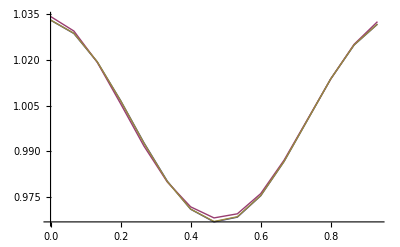

```mathematica
ListLinePlot[{Slab[dataExact,All,0,0],Slab[dataLow,All,0,0],Slab[dataHigh,All,0,0]}]
```

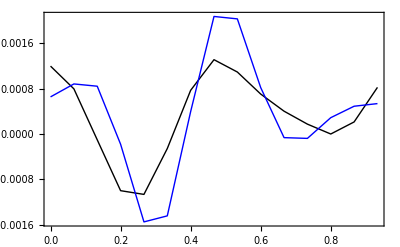

```mathematica
PresentationListLinePlot[{Slab[errLow,All,0,0],2^4Slab[errHigh,All,0,0]}]
```

## Compare

```mathematica
Manipulate[PresentationListLinePlot[
SliceData[SliceData[#,3,z2],2,y2]&/@
{evalOnGrid[exact,{t,x,y,z},ReadGridFunction[runLow,file,i]],
ReadGridFunction[runLow,file,i],
ReadGridFunction[runHigh,file,2i]},
FrameLabel->{"x","g_xx"},PlotRange->Automatic (*{{0,1},2 {-1,1}10^-1}*)],{{z2,0},min,max},{{y2,0},min,max},{i,0,itLow,1}]
```

Invalid arguments to SliceData
Called as SliceData[exact, 3, 0]

Iteration 30 not found in gxx.h5 in run sgw3d_Carlile_ord4_15